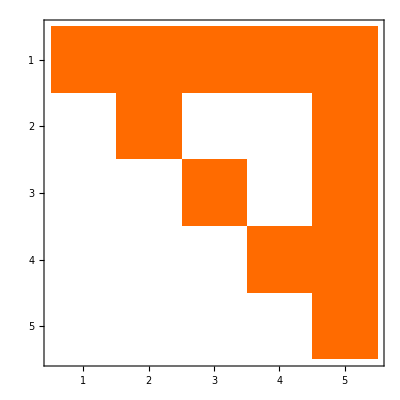

```mathematica
MatrixPlot[ConversionMatrix3["E","C"]]
```

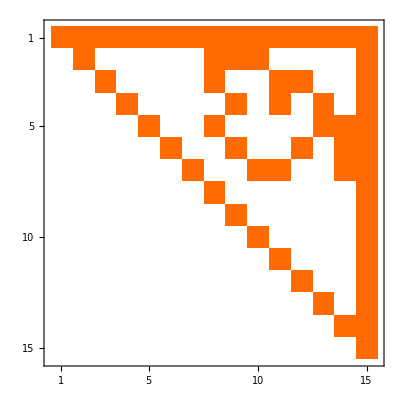

```mathematica
MatrixPlot[ConversionMatrix4["E","C"]]
```

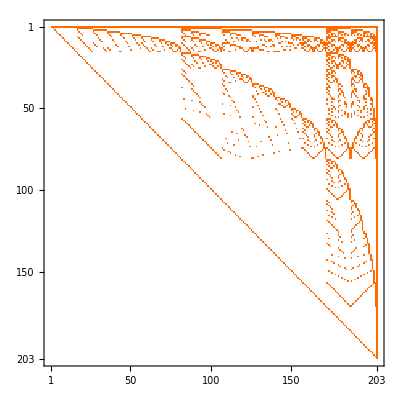

```mathematica
MatrixPlot[ConversionMatrix6["E","C"]]
```

```mathematica
Select[Eigenvectors[ConversionMatrix["E","C"]],#!={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}&]//Length
```

25

```mathematica
Select[Eigenvectors[ConversionMatrix6["E","C"]],#≠Table[0,{k,203}]&]//Length
```

90

```mathematica
Select[Eigenvectors[ConversionMatrix6["E","C"]],#≠Table[0,{k,203}]&]//Length
```

90

```mathematica
Select[Eigenvectors[ConversionMatrix4["E","C"]],#≠Table[0,{k,15}]&]//Length
```

7

```mathematica
Select[Eigenvectors[ConversionMatrix3["E","C"]],#≠Table[0,{k,5}]&]//Length
```

3

```mathematica
z7=ZetaP[setp7];
```

```mathematica
Z7e=Eigenvectors[z7];
```

```mathematica
BellB[7]
```

877

```mathematica
Length[Z7e]
```

877

```mathematica
StirlingS2[7,5]
```

140

```mathematica
StirlingS2[7,4]
```

350

```mathematica
StirlingS2[7,3]
```

301

```mathematica
Select[Z7e,#≠Table[0,{k,BellB[7]}]&]//Length
```

371

```mathematica
z8=ZetaP[setp8];
```

```mathematica
Z8e=Eigenvectors[z8];
```

```mathematica
BellB[8]
```

4140

```mathematica
Select[Z8e,#≠Table[0,{k,BellB[8]}]&]//Length
```

1708

```mathematica
Table[StirlingS2[7,k],{k,7}]
```

{1,63,301,350,140,21,1}

```mathematica
301+140
```

441

```mathematica
z6=ZetaP[setp6];
```

```mathematica
Z6e=Eigenvectors[z6];
```

```mathematica
BellB[6]
```

203

```mathematica
StirlingS2[6,3]
```

90

```mathematica
Select[Z6e,#≠Table[0,{k,BellB[6]}]&]//Length
```

90

```mathematica
StirlingS2[3,2]
```

3

```mathematica
StirlingS2[4,2]
```

7

```mathematica
StirlingS2[5,3]
```

25

```mathematica
StirlingS2[6,3]
```

90

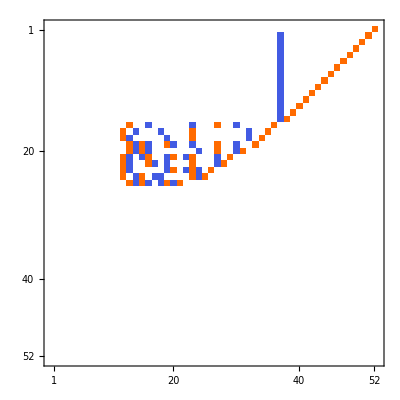

```mathematica
Eigensystem[ConversionMatrix["G","C"]][[2]]//MatrixPlot
```

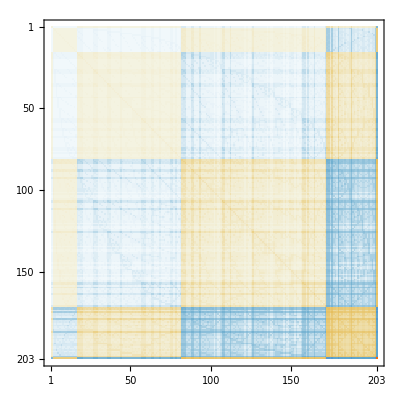

```mathematica
Inverse[ConversionMatrix6["E","C"].ConversionMatrix6["G","C"]]//MatrixPlot
```

```mathematica
allBases6
```

{C,E,G,F}

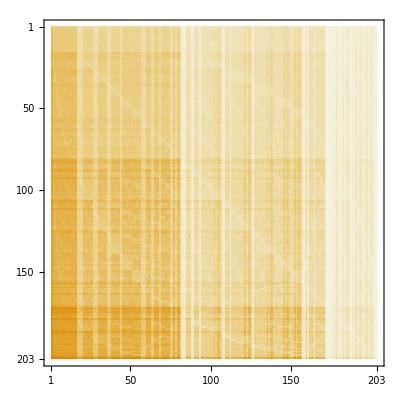

```mathematica
MatrixPlot[ConversionMatrix6["G","C"].ConversionMatrix6["E","C"].ConversionMatrix6["F","C"]]
```